```mathematica
<<Geometry`
```

## AppBladeTiling

### Code

```mathematica
bladeTiling[fig_]:=Module[
	{nPos0,nPos,out},
	nPos0={Max[Cases[fig,pnt,Infinity][[All,1]]],Max[Cases[fig,pnt,Infinity][[All,2]]]/2};
	nPos={Max[Cases[fig,pnt,Infinity][[All,1]]],Max[Cases[fig,pnt,Infinity][[All,1]]]};
	out={fig,tra3[fig,nPos],ref3[{tra3[fig,nPos]},{{0,1},{1,1}}],ref3[ref3[tra3[fig,nPos],{{0,1},{1,1}}],{{1,1},{1,0}}]}
]
blade:={{{1,{{0,0},{1,0},{1,2},{0,1}}},{LightBlue,.25}},{Black,1,.0025,2 π,2 π}}
showBlade[n_]:=Nest[bladeTiling,blade,n]
```

### GUI

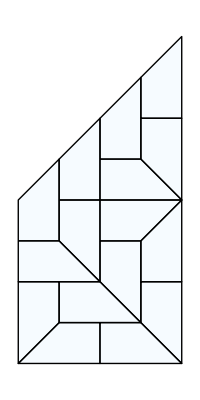

```mathematica
showBlade[2]//toGL//gr
```